## Partial-Wave Scattering

Yen Lee Loh.  Touched 2010, 2010-6-12.
Not complete yet.

This requires the following package:

```mathematica
<<"./yllutils.m";
```

Get::noopen: Cannot open yllutils.m.

## Section Extra setup

Let us define short aliases for Mathematica's spherical Bessel, Neumann, and Hankel functions:

```mathematica
Clear[l,p,j,y,H,h,jprime,yprime]
j[l_,p_]=SphericalBesselJ[l,p]//FullSimplify;
y[l_,p_]=SphericalBesselY[l,p]//FullSimplify;
H[l_,p_]=SphericalHankelH1[l,p]//FullSimplify;
h[l_,p_]=SphericalHankelH2[l,p]//FullSimplify;
jprime[l_,p_]=D[SphericalBesselJ[l,p], p]//FullSimplify
yprime[l_,p_]=D[SphericalBesselY[l,p], p]//FullSimplify
Hprime[l_,p_]=D[SphericalHankelH1[l,p], p]//Simplify
```

(l SphericalBesselJ[l,p])/p-SphericalBesselJ[1+l,p]

(l SphericalBesselY[l,p])/p-SphericalBesselY[1+l,p]

1/2 (SphericalHankelH1[-1+l,p]-(SphericalHankelH1[l,p]+p SphericalHankelH1[1+l,p])/p)

Also define the following:

```mathematica
solvePartialWave[l_,p_,q_]:=Module[{δ,b},
δ=ArcTan[q y[l,p]jprime[l,q]-p j[l,q]yprime[l,p],p j[l,q]jprime[l,p]-q j[l,p]jprime[l,q]];
b=(Cos[δ]j[l,p]+Sin[δ]y[l,p])/j[l,q];
Return[{δ,b}];
];
```

## Section Partial-Wave Scattering Theory

### Section.Subsection Radial Schrödinger Equation for Spherically Symmetric Potential

Consider a scalar, non-relativistic, quantum mechanical particle in a 3D continuum, with a spherically symmetric potential V(r).  The Schrödinger equation is
	-1/(2m)∇^2 ψ+V(r)ψ=Eψ
	∴ -∇^2 ψ+k^2 ψ=0
where k^2(r)=2m[E-V(r)].  Separation of variables in spherical polars gives
	ψ(r,θ,ϕ)=∑_lm ψ_lm R(r)Y_lm(θ,ϕ)
where Y_lm(θ,ϕ) are spherical harmonic functions, and the radial wavefunction R(r) satisfies the radial equation
	(∂_r)^2(rR)+[k^2(r)-(l(l+1))/r^2]rR=0.

### Section.Subsection Radial Wavefunctions in a Region of Constant Potential: Bessel, Neumann, and Hankel Functions

For a constant potential V(r)=V, the local wavenumber is k(r)=k=√(2m(E-V)), and R(r) obeys the spherical Bessel differential equation
	(∂_r)^2(rR)+[k^2-(l(l+1))/r^2]rR=0.
The solutions are spherical Bessel and Neumann functions, or, equivalently, spherical incoming and outgoing Hankel functions.
In the setup section we have defined the following aliases for the builtin Mathematica  functions: j[l,p],y[l,p],H[l,p],h[l,p],jprime,yprime,Hprime.
The Hankel functions of the second kind,  h_l(r)=SphericalHankelH2[l,r]~e^-ir, represent incoming spherical waves,
whereas the Hankel functions of the first kind,  h_l(r)=SphericalHankelH1[l,r]~e^(+ir), represent outgoing spherical waves.

The spherical Bessel, Neumann, and Hankel functions of integer argument can be written in terms of trigonometric or exponential functions.  BesselJ corresponds to sin, BesselY corresponds to cos, H=H1 corresponds to exp ikr, and h=H2 corresponds to exp (-ikr).  Bound states are most conveniently written in terms of H(i λ r)~ exp(-λ r).

```mathematica
FunctionExpand/@{
j[0,r],y[0,r],H[0,r],h[0,r],H[0,I r],h[0,I r]}
```

{Sin[r]/r,-Cos[r]/r,-(ⅈ ⅇ^(ⅈ r))/r,(ⅈ ⅇ^(-ⅈ r))/r,-ⅇ^-r/r,ⅇ^r/r}

### Section.Subsection The Wavefunction at Zero Incident Energy: Laplace's Equation

In the limit k→0, the Schrödinger equation is simply Laplace's equation,
	-∇^2 ψ+k^2 ψ=0.
Hence the radial equation is
	(∂_r)^2(rR)-(l(l+1))/r^2 rR=0.
The solutions are
	R=A r^l+B r^(-l-1).

You can check that the spherical Bessel functions reduce to power laws in the limit k→0.  For example, in the s-wave channel (l=0), j_l(kr)=(sin kr)/kr→1 and y_l(kr)=-(cos kr)/kr→-1/kr, so the general soluation is simply R(r)=A+B/r.

## Section Partial-Wave Scattering Theory for a Flat Barrier or Well

### Section.Subsection Cartoon

In this section we consider a scattering experiment as depicted more or less as in the following cartoon:

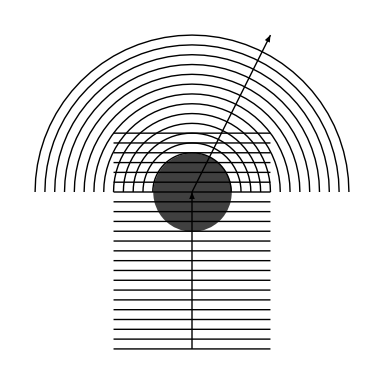

```mathematica
myRange={{-1,1},{-1,1}}*4;
Show[
(*ArrayPlot[Reverse@Transpose@Table[Cos[2π y]Exp[-0.5(x/1)^2],{x,-5,5,.03},{y,-5,5,.03}],
DataRange->myRange,ColorFunction->"BlueGreenYellow",ColorFunctionScaling->True],*)
Graphics[{
Table[Line@{{-2,y},{2,y}},{y,-5,1.5,.25}],
Table[Circle[{0,0},r,{0,π}],{r,1,4,.25}]
}],
Epilog->{
Thick,Black,Arrow@{{0,-4},{0,0}},Arrow@{{0,0},{2,4}},
Opacity[0.75,Black],Disk[]
},
PlotRange->myRange,ImageSize->384,AspectRatio->Automatic,Frame->None
]
```

The general strategy is to decompose the incident wave into partial waves (spherical harmonics), calculate the phase shift for each partial wave, and finally recombine the scattered partial waves.

### Section.Subsection Low-energy scattering for General l

Now consider a potential that is a piecewise constant function, such that the potential is V within a sphere of radius 1 and zero outside:
	V(r)=Piecewise[{{r<1, V}, {r>1, 0.}}]
We have taken the radius of the potential, r_0, to be the length unit.  Thus, all wavevectors will be measured in units of 1/r_0, and all energies will be measured in units of ℏ^2/m r_0.

Let us solve the Schrödinger equation for an incident particle of zero energy, E=0.  
First, consider the case of a potential well (V < 0).  Then the wavenumber inside the barrier, q=√(-2mV), is a real number.  Outside the barrier the wavefunction satisfies Laplace's equation.  The solution is of the form
	R(r)=Piecewise[{{r<1, Aj(qr)+By(qr)}, {r>1, C r^l+Dr^(-l-1).}}]
(We will omit the subscripts l  on the spherical Bessel functions.)   
The wavefunction must be regular at r=0, so B=0.  Let us choose A=1.  At the boundary r=1, the wavefunction and its derivative must be continuous, R_-(r)=R_+(r) and R_-'(r)=R_+'(r):
	{j(q)=C+D
qj'(q)=lC-(l+1)D.
Thus,
	{C=((l+1)j(q)+qj'(q))/(2l+1)
D=(l j(q)-qj'(q))/(2l+1).
So,
	R(r)=Piecewise[{{r<1, j(qr)}, {r>1, ((l+1)j(q)+qj'(q))/(2l+1)r^l+(l j(q)-qj'(q))/(2l+1)r^(-l-1).}}]
	
Now, in the case of a potential barrier (V>0), we can write q=iλ where λ=√(2mV).  The final expression for the wavefunction involves spherical Bessel functions of imaginary argument.  This happens to work just fine in Mathematica, so we don't need to do any hacking.

#### Start working

```mathematica
Solve[{c+d==jq,l c-(l+1)d==qjpq},{c,d}]//Simplify
```

{{c→(jq+jq l+qjpq)/(1+2 l),d→(jq l-qjpq)/(1+2 l)}}

```mathematica
Clear[q,λ]
SphericalBesselJ[l,q]//FunctionExpand
SphericalBesselJ[l,I λ]//FunctionExpand
SphericalBesselJ[0,I λ]//FunctionExpand//ComplexExpand//Simplify(*GACK, doesn't work *)
```

(√(π/2) BesselJ[1/2 (1+2 l),q])/(√q)

√(π/2) (ⅈ λ)^(-1/2+1/2 (1+2 l)) λ^(1/2 (-1-2 l)) BesselI[1/2 (1+2 l),λ]

Sinh[λ]/λ

#### End working

```mathematica
Clear[l,k,p,q,V];
rmax=5;
Manipulate[
q=√(-2V);
Show[
ListPlot[{{0,V},{1,V},{1,0},{rmax,0}},PlotStyle->Thick],
Plot[0,{r,0,rmax},PlotStyle->Dashed],
Plot[j[l,q r],{r,0,1},PlotStyle->{{Thick,Red}},PlotRange->All],
Plot[((l+1)j[l,q]+q jprime[l,q])/(2l+1)r^l+(l j[l,q]-q jprime[l,q])/(2l+1)r^(-l-1),{r,1,rmax},PlotStyle->{{Thick,Red}},Exclusions->None],
GridLines->{{0,1},{0}},
PlotRange->{{0,rmax},{-2,5}},PlotRangePadding->None,FrameLabel->{"r","R(r)\nV(r)"},
ImageSize->{768,384}
],
{{V,0.1},-50,4,Appearance->"Open"},
{{l,0},0,10,1,Appearance->"Open"},
ControlPlacement->Left
]
```

Plot::plln: Limiting value rmax in {r, 0, rmax} is not a machine-size real number.

Plot::plln: Limiting value rmax in {r, 1, rmax} is not a machine-size real number.

Show::gcomb: Could not combine the graphics objects in Show[GraphicsBox[List[List[List[], List[Hue[0.67`, 0.6`, 0.6`], Thickness[Large], PointBox[List[List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]]]]], List[]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[0.`, 1.`], List[0.`, 0.1`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]], Plot[0, {r, 0, rmax}, PlotStyle → Dashed], « 6 », ImageSize → {768, 384}].

Plot::plln: Limiting value rmax in {r, 0, rmax} is not a machine-size real number.

General::stop: Further output of Plot will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[GraphicsBox[List[List[List[], List[Hue[0.67`, 0.6`, 0.6`], Thickness[Large], PointBox[List[List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]]]]], List[]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[0.`, 1.`], List[0.`, 0.1`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]], Plot[0, {r, 0, rmax}, PlotStyle → Dashed], « 6 », ImageSize → {768, 384}].

### Section.Subsection Low-energy scattering for l=0 (s-wave scattering)

The above applet was not very illuminating.  To get more intuition, let us focus on s-wave scattering lengths (l=0).  Furthermore, let us work with rR(r).  Repeating the algebra,
	rR(r)=Piecewise[{{r<1, A sin qr-B cosqr}, {r>1, Cr+D.}}]
The wavefunction R(r) must be regular at r=0, so rR(r) must be zero, and soB=0.  Let us choose A=1.  At the boundary r=1, the wavefunction and its derivative must be continuous, so
	{sin q=C+D
q cos q=C.
Therefore, C = q cos q  and  D=sin q-q cos q.  After a little algebra, we can put the wavefunction in the form
	rR(r)=Piecewise[{{r<1, sin qr}, {r>1, (q cos q)[r-(1-(tan q)/q)].}}]
This has a simple geometrical interpretation.  Given the depth of the potential well -V, we know the wavenumber inside the well q=√(2mV).  Thus, draw a sine wave in the region 0<r<1.  Draw the tangent line to this sine wave at r=1 and extend it to ±∞.  The s-wave scattering length a_s is defined as the intercept of the tangent with the r axis.  From the form above, it is obvious that a_s=1-(tan q)/q.  This can have either sign.
	
In the case of a potential barrier (V>0), we can write q=iλ where λ=√(2mV), but it will be convenient to redefine the wavefunction so that it is real-valued.  Furthermore, in order to avoid the wavefunction shooting off to infinity, it will be convenient to choose the normalization such that C=1 (instead of using A=1 as before).  Then, the wavefunction is
	rR(r)=Piecewise[{{r<1, (sinh λr)/(λ cosh λ)}, {r>1, r-(1-(tanh λ)/λ).}}]
The scattering length is a_s=1-(tanh λ)/λ, which is a positive number.

As you play with the applet below, watch how the scattering length sweeps from -∞ to +∞ as the well depth is varied.

```mathematica
Clear[l,k,p,q,V,λ];
rmax=5;
Manipulate[
Show[
ListPlot[{{0,V},{1,V},{1,0},{rmax,0}},PlotStyle->Thick],
Which[
(*-------- potential well --------*)
V<0,
q=√(-2V);{
Plot[Sin[q r],{r,0,1},PlotStyle->{{Thick,Red}},PlotRange->All],
Plot[Sin[q]+q Cos[q](r-1),{r,1,rmax},PlotStyle->{{Thick,Red}}],
Plot[Sin[q]+q Cos[q](r-1),{r,-rmax,rmax},PlotStyle->{{Dashed,Black}}],
Graphics[{Black,AbsolutePointSize@8,Point@{1-Tan[q]/q,0}}]
},
(*-------- potential barrier --------*)
V>0,
λ=√(2V);{
Plot[Sinh[λ r]/(λ Cosh[λ]),{r,0,1},PlotStyle->{{Thick,Red}},PlotRange->All],
Plot[r-(1-Tanh[λ]/λ),{r,1,rmax},PlotStyle->{{Thick,Red}}],
Plot[r-(1-Tanh[λ]/λ),{r,-rmax,rmax},PlotStyle->{{Dashed,Black}}],
Graphics[{Black,AbsolutePointSize@8,Point@{1-Tanh[λ]/λ,0}}]
},
(*-------- no potential --------*)
True,
q=0;{
Plot[r,{r,0,1},PlotStyle->{{Thick,Red}},PlotRange->All],
Plot[r,{r,1,rmax},PlotStyle->{{Thick,Red}}],
Plot[r,{r,-rmax,rmax},PlotStyle->{{Dashed,Black}}],
Graphics[{Black,AbsolutePointSize@8,Point@{0,0}}]
}
],
GridLines->{{0,1},{0}},
PlotRange->{{-rmax,rmax},{-2,2}},PlotRangePadding->None,FrameLabel->{"r","rR(r)\nV(r)"},
ImageSize->{768,384}
],
{{V,-1},-20,20,Appearance->"Open"},
{{l,0},0,10,1,Appearance->"Open"},
ControlPlacement->Left,TrackedSymbols:>{V,l}
]
```

### Section.Subsection Scattering length a_s

For a flat barrier or well, the scattering length is a_s=1-(tanh λ)/λ where λ=√(2mV).  We plot this below.  Note that a_s→r_0 for very high barriers; that is, a hard core scatterer has a scattering length that is equal to its radius.  (Remember that we are measuring lengths in units of r_0.)  For potential wells (V<0), a_s can have either sign.  The poles correspond to bound states.

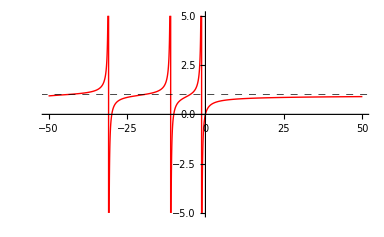

```mathematica
Plot[1-Tanh[√(2V)]/(√(2V)),{V,-50,50},PlotRange->{-5,5},PlotRangePadding->0,
PlotStyle->{{Thick,Red}},GridLines->{{0},{0,{1,Dashed}}},GridLinesStyle->Black,FrameLabel->{"V","a_s"}]
```

### Section.Subsection Wavefunction and phase shifts for arbitrary energies

Our potential is a piecewise function
	V(r)=Piecewise[{{r<1, V}, {r>1, 0.}}]
Now let us solve the Schrödinger equation for an incident particle of energy E.  Proceed in the usual manner for an ODE with piecewise coefficients.  In each region, the radial equation for the lth partial wave is a spherical Bessel equation.  At each boundary, provided that k(r) is integrable, then (rR) and ∂_r (rR) must be continuous.  This implies that R and ∂_r R must both be continuous.  Thus we match wavefunctions and derivatives.  Putting this together,
	{r<1 |   | (∂_r)^2(rR)+[q^2-(l(l+1))/r^2]rR=0
r>1 |   | (∂_r)^2(rR)+[p^2-(l(l+1))/r^2]rR=0
r=0 |   | R(r) finite
r=1 |   | R(1^-)=R(1^+)
  |   | ∂_r R(1^-)=∂_r R(1^+)
where the wavenumbers outside and inside the barrier are  p=√(2mE) and q=√(2m(E-V_0)).  The usual algebra shows that
	R(r)=Piecewise[{{r<1, bj(qr)}, {r>1, (cos δ)j(pr)+(sin δ)y(pr)}}]
where
	b=(cj(p)+sy(p))/(j(q)),
	 tan δ=(pj(q)j'(p)-qj'(q)j(p))/(qj'(q)y(p)-pj(q)y'(p)).
For positive-energy scattering states, this normalization corresponds to unit incident flux in the l  angular momentum channel.  The phase shift δ depends on l, of course.

For negative energies E<0, we will rescale the above wavefunction by an additional factor of  1/(b j_0(q r)) for plotting purposes.  For l=0, this normalizes the wavefunction such that R(0)=1, and it also cures some problems resulting from complex numbers.

#### Start detailed working

The solution is of the form
	R(r)=Piecewise[{{r<1, Aj(qr)+By(qr)}, {r>1, Cj(pr)+Dy(pr).}}]
In fact, it will be convenient to write
	R(r)=Piecewise[{{r<1, bj(qr)}, {r>1, cj(pr)+sy(pr).}}]
which contains three unknowns b, c, and s.  We shall choose the normalization such that c^2+s^2=1, so that c=cos δ and s=sin δ.  For positive-energy scattering states, this normalization corresponds to unit incident flux in the l channel.  Matching wavefunctions and derivatives gives
	{bj(q)=cj(p)+sy(p)
qbj'(q)=p[cj'(p)+sy'(p)].
Solve for the unknowns:
	bj(q)×p[cj'(p)+sy'(p)]=qbj'(q)×[cj(p)+sy(p)]
∴ c[pj(q)j'(p)-qj'(q)j(p)]=s[qj'(q)y(p)-pj(q)y'(p)]
∴ tan δ=(pj(q)j'(p)-qj'(q)j(p))/(qj'(q)y(p)-pj(q)y'(p))
and then
	b=(cj(p)+sy(p))/(j(q)).

#### End detailed working

```mathematica
solvePartialWave[l_,p_,q_]:=Module[{δ,b},
δ=ArcTan[q y[l,p]jprime[l,q]-p j[l,q]yprime[l,p],p j[l,q]jprime[l,p]-q j[l,p]jprime[l,q]];
(*δ=ArcTan[(p j[l,q]jprime[l,p]-q j[l,p]jprime[l,q])/(q y[l,p]jprime[l,q]-p j[l,q]yprime[l,p])];*)
b=(Cos[δ]j[l,p]+Sin[δ]y[l,p])/j[l,q];
Return[{δ,b}];
];
```

```mathematica
solvePartialWave[0,1.0I,2.0]
```

{1.5708+2.55935 ⅈ,-1.46089×10^-14+5.46136 ⅈ}

```mathematica
TableForm[
Table[{l,Sequence@@solvePartialWave[l,0.1,0.6]},{l,0,10}]
,TableHeadings->{{},{"l","δ_l","b_l"}}
]
```

| l | δ_l | b_l
 | 0 | 3.12806 | -1.20383
 | 1 | 3.14158 | -0.176822
 | 2 | 3.14159 | -0.0287728
 | 3 | 3.14159 | -0.0047472
 | 4 | 3.14159 | -0.000793533
 | 5 | 3.14159 | -0.0158257
 | 6 | 3.14159 | -37.3343
 | 7 | 3.14159 | -121157.
 | 8 | 3.14159 | -5.14315×10^8
 | 9 | 3.14159 | -2.76612×10^12
 | 10 | 3.14159 | -1.83804×10^16

```mathematica
Clear[l,k,p,q,V,ε];
rmax=5;
Manipulate[
If[ε==0.,ε=0.00001];If[ε==V,ε+=0.00001];p=√(2ε);q=√(2(ε-V));
{δ,b}=solvePartialWave[l,p,q];If[ε>0,A=-1.,A=1/(b j[l,0])];
Column@{
Show[
Plot[ε,{r,0,rmax},PlotStyle->Dashed],
ListPlot[{{0,V},{1,V},{1,0},{rmax,0}},PlotStyle->Thick],
GridLines->{{1},{0}},
PlotRange->{All,{-10,10}},PlotRangePadding->0,FrameLabel->{"","V(r)"},
ImageSize->{768,256},ImagePadding->{{All,All},{32,8}}
],
Show[
Plot[Re[A b j[l,q r]],{r,0,1},PlotStyle->{{Thick,Red}},Exclusions->None],
Plot[Re[A(Cos[δ] j[l,p r]+Sin[δ] y[l,p r])],{r,1,rmax},PlotStyle->{{Thick,Red}},Exclusions->None],
GridLines->{{1},{0}},
PlotRange->{{0,rmax},{-1.5,3}},PlotRangePadding->0,FrameLabel->{"r","R(r)"},
ImageSize->{768,256}
]
},
{{V,-4.},-10,10,Appearance->"Open"},
{{ε,4.},-5,10,Appearance->"Open"},
{{l,0},0,10,1,Appearance->"Open"},(*{{A,4.},0,10,Appearance->"Open"},*)
ControlPlacement->Left
]
```

### Section.Subsection Bound states for general l

#### Section.Subsection.Subsubsection Solving the eigenproblem

Now let us calculate the bound state energies and wavefunctions.  This is an eigenproblem, which is more tricky than the scattering problem earlier.
If the potential in the well is V, it is reasonable to expect that the bound state energy will be in the range V<E<0.  Thus it will be convenient to work with the decay length in free space λ=√(-2mE) and the wavenumber in the well q=√(2m(E-V)).  Now, remember that H(iλr) behaves like e^-λr, whereas h(iλr) behaves like e^(+λr), which would not be admissible.  Therefore the wavefunction must have the following form:
	R(r)=Piecewise[{{r<1, A j(qr)}, {r>1, B H(iλr).}}]
Let A=1.  Match the wavefunctions at r=1.  Thus, the wavefunction must be
	R(r)=Piecewise[{{r<1, j(qr)}, {r>1, (j(q))/(H(iλ))H(iλr).}}]
Matching the derivatives at r=1 leads to an additional condition,
	λ j(q) iH'(iλ)=q j'(q)H(iλ).
Define the residual as
	residual=(q j'(q))/λ-(iH'(iλ) j(q))/(H(iλ)).
With this definition, both j and j' appear in the numerator rather than the denominator, so that the residual does not have poles.  Furthermore, the exponential behavior of H and H' cancels out, so that the residual is of manageable magnitude:

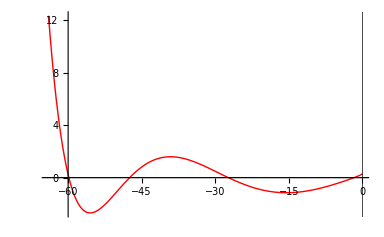

```mathematica
Clear[ε,V,l,λ,q,residual];
l=0;
V=-64.;
residual[ε_Real]=Re[q*jprime[l,q]-(λ*I*Hprime[l,I λ]*j[l,q])/H[l,I λ]]/.{λ->√(-2ε),q->√(2(ε-V))};
Plot[
residual[ε],{ε,V,0},
PlotRange->All,PlotRangePadding->{0,Scaled@0.02},
PlotStyle->{{Thick,Red}},GridLines->{{0},{0}},GridLinesStyle->Black,FrameLabel->{"E","residual"},RotateLabel->True]
```

Each zero of the residual corresponds to a bound state.  (Remember that the unit of energy is ℏ^2/(m r_0^2).)  For V=-100, in the l=0 channel, there are four bound states.  Let us find their energies explicitly:

```mathematica
(*-------- Find zero crossings approximately --------*)
εOld=V;
sOld=Sign[residual[εOld]];
εbrackets={};
Do[
s=Sign[residual[ε]];
If[s≠sOld,AppendTo[εbrackets,{εOld,ε}]];
εOld=ε;sOld=s;
,{ε,V+0.1,Abs[V]/100.,1.}];
εbrackets
(*-------- Refine --------*)
εlist=Table[
ε/.FindRoot[residual[ε],{ε,Sequence@@εbracket},AccuracyGoal->5,MaxIterations->1000],
{εbracket,εbrackets}]
```

{{-59.9,-58.9},{-47.9,-46.9},{-27.9,-26.9},{-1.9,-0.9}}

{-59.8417,-47.4685,-27.3129,-1.72284}

#### Section.Subsection.Subsubsection Visualize the eigenenergies and wavefunctions

```mathematica
Rr[r_,V_,ε_]:=Piecewise[{
{j[l,q r],r≤1},
{Re[j[l,q]/H[l,I λ] H[l,I λ r]],r>1}
}]/.{λ->√(-2ε),q->√(2(ε-V))};
```

```mathematica
boundStateEnergyPlot=Show[
Plot[0,{r,0,2},PlotStyle->None,FillingStyle->LightGray,Filling->Top,PlotRange->{{0,2},{-1.1Abs@V,0.2Abs@V}}],
ListPlot[{{0,V},{1,V},{1,0},{2,0}},PlotStyle->{{Thick,Black}}],
Plot[εlist,{r,0,1},PlotStyle->(Directive@{Thick,Dashed,#}&/@alternateColorList)],
Epilog->{
Table[{alternateColorList⟦n⟧,Text[εlist⟦n⟧,{1.05,εlist⟦n⟧},Left]},{n,Length@εlist}],
Text["continuum",{0.5,10}]
},
PlotRange->{{0,2},{-1.1Abs@V,0.2Abs@V}},
PlotRangePadding->0,
Frame->False,Axes->True,AxesOrigin->{0,0},Ticks->{None,Automatic},AxesLabel->{"r","E_n"},
GridLines->{{0},{}}
];
```

Graphics::gprim: alternateColorList was encountered where a Graphics primitive or directive was expected.

General::stop: Further output of Graphics will be suppressed during this calculation.

Part::partd: Part specification alternateColorList ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification alternateColorList ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification alternateColorList ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part will be suppressed during this calculation.

```mathematica
boundStateWavefunctionPlot=Plot[Rr[r,V,#]&/@εlist//Evaluate,{r,0,1,2},PlotStyle->(Directive@{Thick,#}&/@alternateColorList),
Frame->False,Axes->True,AxesOrigin->{0,0},GridLines->{{1},{}},GridLinesStyle->Directive@{Dashed,Black},
PlotRange->All,PlotRangePadding->{0,Scaled@0.02},
AxesLabel->{"r","R_n(r)"}];
```

Graphics::gprim: alternateColorList was encountered where a Graphics primitive or directive was expected.

General::stop: Further output of Graphics will be suppressed during this calculation.

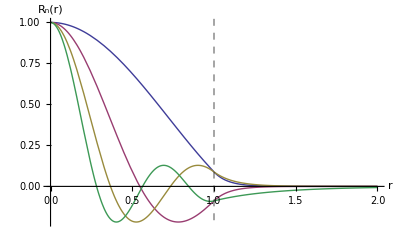
-Graphics--Graphics-

```mathematica
Row@{boundStateEnergyPlot,boundStateWavefunctionPlot}
```

For the particular example under consideration, note that E_4 is close to zero, and so R_4(r) is quite long-ranged.

#### Section.Subsection.Subsubsection Bound state energies as a function of well depth

ContourPlot is a simple way to generate a plot of bound state energies as a function of well depth:

```mathematica
Clear[ε,V,l,λ,q,residual];
residual[l_,V_,ε_]=Re[q*jprime[l,q]/λ-(I*Hprime[l,I λ]*j[l,q])/H[l,I λ]]/.{λ->√(-2ε),q->√(2(ε-V))};
```

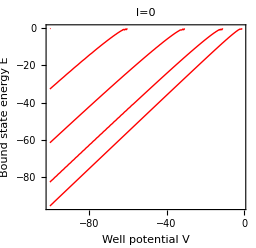

```mathematica
ContourPlot[
residual[0,V,ε],{V,-100.,-0.01},{ε,-99.,-0.001},Contours->{0},
PlotRangePadding->0,ImageSize->256,AspectRatio->Automatic,ContourShading->None,ContourStyle->Directive@{Thick,Red},
PlotRange->All,
FrameLabel->{"Well potential V","Bound state energy E"},RotateLabel->True,
PlotLabel->"l=0"
]
```

### Section.Subsection Bound states for l=0

Here is a more analytic working for purists.  Consider the s-wave channel (l=0), and write out the solutions in terms of trigonometrics and exponentials:
	rR(r)=Piecewise[{{r<1, A sin qr}, {r>1, B e^-λr.}}]
Choosing A=1 and matching the wavefunction at r=1, we have
	rR(r)=Piecewise[{{r<1, sin qr}, {r>1, e^(λ(1-r))sin q.}}]
Matching derivatives leads to the additional condition
	λ=-q cot q
where λ>0.  This implies that the solutions are of the form
	q=s+nπ
where 0<s<π/2 and n  is an integer.  We can generate the solution curves as follows:

	For n=1,2,3,4,5,6 
	For s=0 to π/2
	Find q=s+nπ, λ=-q cot q, E=-λ^2/2, and V=-(λ^2+q^2)/2
	Plot bound state energy E as a function of well potential V.

Part::partd: Part specification myStyles ⟦ 2 ⟧ is longer than depth of object.

Graphics::gprim: myStyles ⟦ 2 ⟧ was encountered where a Graphics primitive or directive was expected.

Part::partd: Part specification myStyles ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part will be suppressed during this calculation.

Graphics::gprim: myStyles ⟦ 3 ⟧ was encountered where a Graphics primitive or directive was expected.

Graphics::gprim: myStyles ⟦ 4 ⟧ was encountered where a Graphics primitive or directive was expected.

General::stop: Further output of Graphics will be suppressed during this calculation.

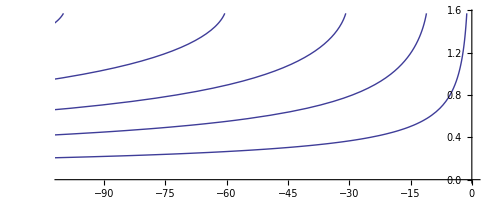

```mathematica
Show[ Table[ParametricPlot[{-((n π-s)^2(1+Cot[s]^2))/2,s},{s,0.0001,π/2-0.0001},PlotStyle->myStyles⟦1+n⟧],{n,1,6}],
FrameLabel->{"V_0","s"},PlotRange->{{-100,0},{0,π/2}},GridLines->{{0},{0,π/2}}]
```

Part::partd: Part specification myStyles ⟦ 2 ⟧ is longer than depth of object.

Graphics::gprim: myStyles ⟦ 2 ⟧ was encountered where a Graphics primitive or directive was expected.

Part::partd: Part specification myStyles ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part will be suppressed during this calculation.

Graphics::gprim: myStyles ⟦ 3 ⟧ was encountered where a Graphics primitive or directive was expected.

Graphics::gprim: myStyles ⟦ 4 ⟧ was encountered where a Graphics primitive or directive was expected.

General::stop: Further output of Graphics will be suppressed during this calculation.

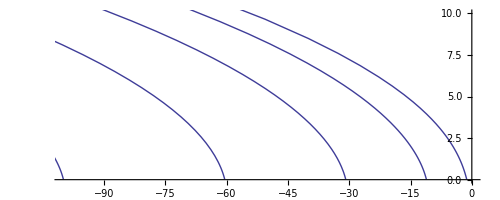

```mathematica
Show[ Table[ParametricPlot[{-((n π-s)^2(1+Cot[s]^2))/2,(n π-s)Cot[s]},{s,0.0001,π/2-0.0001},PlotStyle->myStyles⟦1+n⟧],{n,1,6}],
FrameLabel->{"V_0","λ"},PlotRange->{{-100,0},{0,10}},GridLines->{{0},{0}}]
```

Part::partd: Part specification myStyles ⟦ 2 ⟧ is longer than depth of object.

Graphics::gprim: myStyles ⟦ 2 ⟧ was encountered where a Graphics primitive or directive was expected.

Part::partd: Part specification myStyles ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part will be suppressed during this calculation.

Graphics::gprim: myStyles ⟦ 3 ⟧ was encountered where a Graphics primitive or directive was expected.

Graphics::gprim: myStyles ⟦ 4 ⟧ was encountered where a Graphics primitive or directive was expected.

General::stop: Further output of Graphics will be suppressed during this calculation.

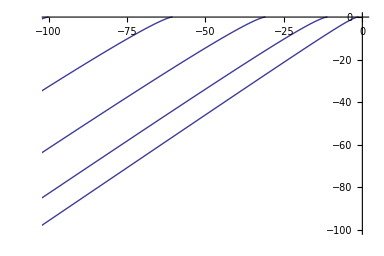

```mathematica
Show[ Table[ParametricPlot[{-((n π-s)^2(1+Cot[s]^2))/2,-((n π-s)Cot[s])^2/2},{s,0.0001,π/2-0.0001},PlotStyle->myStyles⟦1+n⟧],{n,1,6}],
FrameLabel->{"Well potential V","Bound state energy E"},RotateLabel->True,
PlotRange->{{-100,0},{-100,0}},PlotRangePadding->0
]
```

#### Old applet

```mathematica
Clear[l,k,p,q];
rmax=5;
Manipulate[
q=(n π-s);
λ=(n π-s) Cot[s];
b=Exp[-λ]/Sin[q];
Row@{
Show[
Plot[Exp[-λ]Sin[q r],{r,0,1}],
Plot[Sin[q]Exp[-λ r],{r,1,rmax},PlotRange->All],
Frame->False,Axes->True,AxesOrigin->{0,0},GridLines->{{1},{}},GridLinesStyle->Directive@{Dashed,Black},
PlotRange->All,PlotRangePadding->{0,Scaled@0.02},
AxesLabel->{"r","R_n(r)"}]
},
{{n,1},1,10,1,Appearance->"Open"},
{{s,1.4},0.0001,π/2-0.0001,Appearance->"Open"},
ControlPlacement->Left
]
```

### Section.Subsection Scattering of an plane incident wave [this section doesn't work well because DensityPlot is slow]

A plane wave can be expanded in spherical waves.  To be precise, a travelling plane wave of wavevector p, e^-ipz, can be written as a linear combination of standing spherical waves with wavevector p, j_l(pr)P_l(cos θ), with complex coefficients:
	ψ_plane=e^-ipz=∑_l i^l(2l+1)j_l(pr)P_l(cos θ)
where p=√(2mE)  is the wavevector in free space.  We can split this into incoming and outgoing spherical waves, whose radial wavefunctions are h_l  (~e^-ipr) and H_l  (~e^(+ipr)) respectively:
	ψ_plane=∑_l i^l(2l+1)1/2[h_l(pr)+H_l(pr)]P_l(cos θ).
In physical situations, the plane wave is generated by a distant source (such as a neutron beam generated by a reactor).

Now, suppose we introduce a potential V(r) which is short-ranged with a range r_0.  Let us assume that the source is much farther away than r_0, and that the "beam" is wide.  Then the incoming spherical waves will be the same as original.  But the outgoing wave will be modified.  Let each spherical partial wave be modified by a complex factor f:
	ψ_modified=∑_l i^l(2l+1)1/2[h_l(pr)+f_l H_l(pr)]P_l(cos θ)              (r>>r_0)
The factors f_l are a function of the potential V(r) and the incident energy E.

Typically, the potential V(r) is real, so there is no dissipation.  Then, the flux must be conserved.  Therefore, f_l=e^(2i δ_l), where δ_l is called the phase shift.

Okay.  Now expand a plane wave in spherical partial waves:

```mathematica
ψ[r_,θ_]:=Sum[I^l(2l+1)LegendreP[l,Cos[θ]]SphericalBesselJ[l,r],{l,0,10}];
```

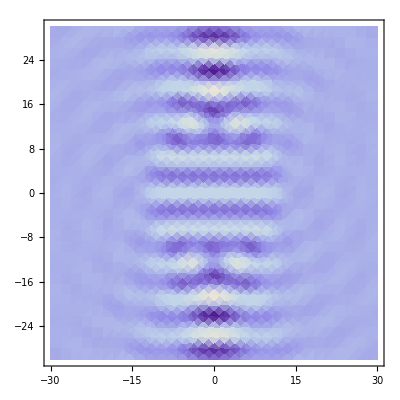

```mathematica
DensityPlot[Re@ψ[√(x^2+z^2),ArcTan[z,x]],{x,-30,30},{z,-30,30},PlotPoints->32,MaxRecursion->1,PlotRange->All]
```

The idea now is to apply the phase shift to each partial wave, so that instead of j_l we have  (cos δ_l)j_l+(sin δ_l)y_l.

```mathematica
p=0.01;
k=0.2;
lmax=50;
δl=Table[
ArcTan[
-p SphericalBesselY[l,k]jprime[l,p]+k yprime[l,k]SphericalBesselJ[l,p],
-k SphericalBesselJ[l,p]jprime[l,k]+p jprime[l,p]SphericalBesselJ[l,k]
],
{l,0,lmax-1}];
cl=Table[
(Cos[δ]SphericalBesselJ[l,k]+Sin[δ]SphericalBesselY[l,k])/SphericalBesselJ[l,p]/.δ->δl⟦1+l⟧,
{l,0,lmax-1}];
TableForm[{Range[0,lmax-1],δl,cl}]//Chop
```

0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49
0.00259803 | 7.02585×10^-6 | 8.05637×10^-9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.980628 | 19.8666 | 398.405 | 7977.22 | 159646. | 3.1942×10^6 | 6.39018×10^7 | 1.2783×10^9 | 2.557×10^10 | 5.11463×10^11 | 1.02303×10^13 | 2.04622×10^14 | 4.09273×10^15 | 8.18595×10^16 | 1.63727×10^18 | 3.27469×10^19 | 6.54964×10^20 | 1.30997×10^22 | 2.62003×10^23 | 5.2402×10^24 | 1.04807×10^26 | 2.09618×10^27 | 4.19244×10^28 | 8.38505×10^29 | 1.67704×10^31 | 3.35413×10^32 | 6.70836×10^33 | 1.34169×10^35 | 2.68342×10^36 | 5.36689×10^37 | 1.07339×10^39 | 2.1468×10^40 | 4.29365×10^41 | 8.58738×10^42 | 1.71749×10^44 | 3.43501×10^45 | 6.87007×10^46 | 1.37402×10^48 | 2.74807×10^49 | 5.49617×10^50 | 1.09924×10^52 | 2.19849×10^53 | 4.39701×10^54 | 8.79408×10^55 | 1.75882×10^57 | 3.51767×10^58 | 7.03537×10^59 | 1.40708×10^61 | 2.81417×10^62 | 5.62837×10^63

(|(2l+1)P_l(cos θ)(1-e^(2iδ))|)^2

The optical sum rule gives the total scattering cross-section σ_total as a sum of partial-wave cross-sections σ_l, which are basically sin^2 δ_l:

```mathematica
σtotal=(4π)/k^2 Sum[(2l+1)Sin[δl⟦1+l⟧]^2,{l,0,lmax-1}]//Chop
```

0.00212054

```mathematica
fθ[θ_]:=1/k Sum[(2l+1)LegendreP[l,Cos[θ]]*Sin[δl⟦1+l⟧]*Exp[I δl⟦1+l⟧]*(1-l/lmax)^2,{l,0,lmax-1}];
```

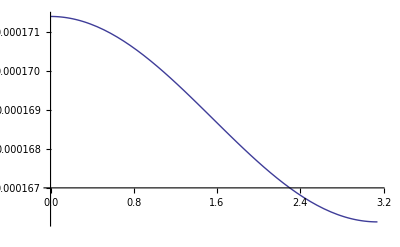

```mathematica
Plot[Abs[fθ[θ]]^2,{θ,0,π},PlotRange->All]
```

```mathematica
ψplane[r_,θ_]:=Sum[I^l(2l+1)LegendreP[l,Cos[θ]]*SphericalBesselJ[l,k r],{l,0,lmax-1}];
ψtot[r_,θ_]:=If[r<1,
Sum[I^l(2l+1)LegendreP[l,Cos[θ]]*
cl⟦1+l⟧*Exp[I δl⟦1+l⟧]*SphericalBesselJ[l,p r],{l,0,lmax-1}],
Sum[I^l(2l+1)LegendreP[l,Cos[θ]]*
(Cos[δl⟦1+l⟧]SphericalBesselJ[l,k r]+Sin[δl⟦1+l⟧]SphericalBesselY[l,k r]),{l,0,lmax-1}]
];
```

```mathematica
sdfsdf=Compile[{{r,_Real},{θ,_Real},{δl,_Real,1},{cl,_Real,1}},
If[r<1,
Sum[I^l(2l+1)LegendreP[l,Cos[θ]]*
cl⟦1+l⟧*Exp[I δl⟦1+l⟧]*SphericalBesselJ[l,p r],{l,0,lmax-1}],
Sum[I^l(2l+1)LegendreP[l,Cos[θ]]*
(Cos[δl⟦1+l⟧]SphericalBesselJ[l,k r]+Sin[δl⟦1+l⟧]SphericalBesselY[l,k r]),{l,0,lmax-1}]
]
];
```

```mathematica
ψtot[r_,θ_]:=sdfsdf[r,θ,δl,cl];
```

```mathematica
xmin=-2.01;xmax=2;xstep=0.1;
```

```mathematica
Timing[asdf=Table[
Re@ψtot[√(x^2+z^2),ArcTan[z,x]],
{x,xmin,xmax,xstep},{z,xmin,xmax,xstep}];]
```

{13.0934,Null}

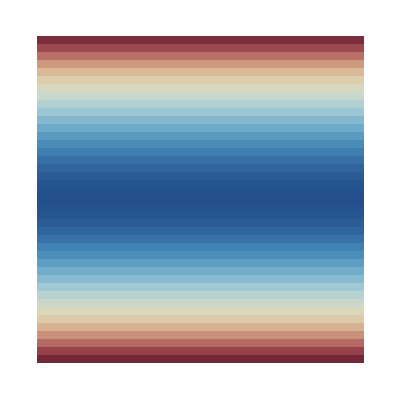

```mathematica
ArrayPlot[Reverse@Transpose@Table[
Re@ψplane[√(x^2+z^2),ArcTan[z,x]],
{x,xmin,xmax,xstep},{z,xmin,xmax,xstep}],
PlotRange->All,PlotRangePadding->None,FrameTicks->None,ColorFunctionScaling->True,ColorFunction->"RedBlueTones"]
```

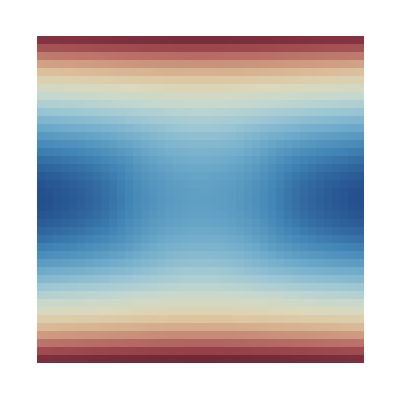

```mathematica
Show[
(*Graphics[{Circle[{0,0},1]}],*)
ArrayPlot[Reverse@Transpose@Table[
Re@ψtot[√(x^2+z^2),ArcTan[z,x]],
{x,xmin,xmax,xstep},{z,xmin,xmax,xstep}],
PlotRange->All,PlotRangePadding->None,FrameTicks->None,ColorFunctionScaling->True,ColorFunction->"RedBlueTones"]
]
```

## Junk and stock

(*δ=ArcTan[
q y[l,p]jprime[l,q]-p j[l,q]yprime[l,p],
p j[l,q]jprime[l,p]-q j[l,p]jprime[l,q]
];*)

It will be convenient to factor as follows: 
	R(r)=A e^-iδ×Piecewise[{{r<1, bj(qr)}, {r>1, e^-iδ h(pr)+e^iδ H(pr)}}]
	=A e^-iδ×Piecewise[{{r<1, bj(qr)}, {r>1, c j(pr)+s y(pr)}}]

where c=cos δ and s=sin δ.  
I might have lost signs and factors.

Across a boundary,
	{R(1^-)=R(1^+)
∂_r R(1^-)=∂_r R(1^+).

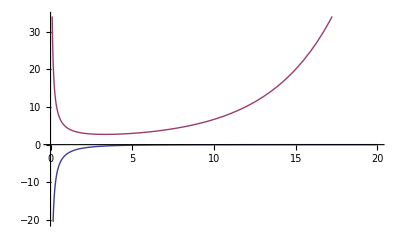

```mathematica
Plot[{
Re@SphericalHankelH1[0,0.3I*r],
Re@SphericalHankelH2[0,0.3I*r]
},{r,0,20}]
```

#### Old version

Now, for a flat barrier of height r  and radius 1, let us solve the Schrödinger equation for an incident particle of energy E.  The wavenumbers outside and inside the barrier are p=√(2mE) and q=√(2m(E-V_0)).  The solution is of the form
	R(r)=Piecewise[{{r<1, Aj(qr)+By(qr)}, {r>1, Cj(pr)+Dy(pr).}}]
In fact,

R(r)=Piecewise[{{r<1, j(qr)}, {r>1, xh(pr)+yH(pr).}}]
Now, for a bound state, the energy is negative, so the free-space wavenumber p  is imaginary: p=iλ.  Therefore the Hankel functions have imaginary arguments:
	R(r)=Piecewise[{{r<1, j(qr)}, {r>1, xh(iλr)+yH(iλr).}}]
Only H is allowed!  So
	R(r)=Piecewise[{{r<1, j(qr)}, {r>1, y H(iλr)}}]
where λ=√(-2mE) and q=√(2m(E-V_0)).  Matching wavefunctions and derivatives at r=1 gives
	{j(q)=yH(iλ)
qj'(q)=iλyH'(iλ)
Therefore
	(iλH'(iλ))/(H(iλ))=(qj'(q))/(j(q)).
Now, for a bound state, λ must be positive.  Therefore the LHS of the equation ... is constrained in a

R(r)=Piecewise[{{r<1, b (sin qr)/qr}, {r>1, (exp -λr)/λr}}]
or to make it even simpler, simply factor out constants and write

## End